# Zika model calibration - Puerto Rico

```mathematica
Quit[]
```

## Setup commands

### Setup base model

#### Headers

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Dropbox\Projects\Zika vaccine\Code\Fresh

```mathematica
If[$CommandLine[[2]]=="-wstp",ClusterRun=False,ClusterRun=True];
```

```mathematica
If[ClusterRun,SetDirectory["./"],SetDirectory[NotebookDirectory[]]];
```

#### File read-in

```mathematica
Import["Zika vaccine model setup.m"]
```

#### Functionality

runCalibration generates a 10-yr time series at weekly steps, taking as input parameters:
1) Country
2) Mosquito-human transmission
3) Human-mosquito transmission
4) (Optionally) any additional parameters to be explicitly specified, in the form {parameterA->parameterAValue, parameterB->parameterBValue, etc}

```mathematica
Clear@runCalibration
runCalibration[country_,betaHV_,parameterOverride_:{}]:=
Block[{basemodel=Get["basemodel"<>country<>".dat"],
startyr=0,endyr=10},
ComputeFinalTimeSeries[
Join[parameterOverride,BaseParameters[country,betaHV]],
Flatten[{NoVaccScen}],
country,startcondsBase[country,startyr,({1,0,0}&),({1,0,0}&),(0&),(0&)],startyr,endyr]
]
```

Compute the cumulative incidence, given a specified human-vector transmission rate and fixing the vector-human transmission rate at 10% greater than human-vector rate

```mathematica
Clear@computeIncidenceByBetaHV
computeIncidenceByBetaHV[country_,betaHV_,parOverride_:{}]:=
With[{calibratedSolution=runCalibration[country,betaHV,parOverride]},
(
With[{infections=pullAllInfections[calibratedSolution]},((*Subtract out the first element of Infections - as this represents the seed infection*)
infections-First[infections])/pullAllPopulation[calibratedSolution]]
)
]
```

Write the computed incidence to file

```mathematica
inputdir=If[ClusterRun,"./",NotebookDirectory[]];
```

```mathematica
outputdir=If[ClusterRun,"./",NotebookDirectory[]<>"/Data/Calibration 2017"];
```

#### Define CHKV data

Setup target distribution for CHKV attack rate

```mathematica
target=BetaDistribution[242,1031-242]
```

BetaDistribution[242,789]

```mathematica
N@Mean@target
```

0.234724

### Read in data

#### Read in CDC data

```mathematica
SetDirectory[NotebookDirectory[]<>"/InputData/PuertoRicoData"]
```

D:\Dropbox\Projects\Zika vaccine\Code\Fresh\InputData\PuertoRicoData

Pull out all CSV files

```mathematica
csvfiles=Select[FileNames[],StringContainsQ[#,".csv"]&];
```

Pull out the date / week the file corresponds to

```mathematica
filedates=Sort[StringTake[#,{11,20}]&/@csvfiles];
```

#### Define CDC epi curve

Define a function to extract the entry for cumulative zika cases in Puerto Rico, for the specified file-date

```mathematica
extractCumulativeZikaCases=(Import["PRDH_Zika_"<>#<>".csv"][[(*3*)5,8]])&;
```

```mathematica
extractCumulativeZikaCases[filedates[[1]]]
```

18

```mathematica
zikaTimeSeries={DateObject[#],extractCumulativeZikaCases[#]}&/@filedates;
```

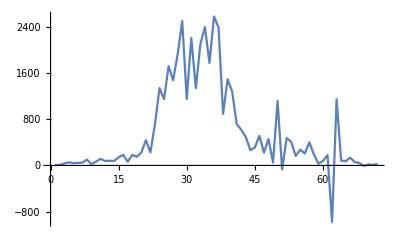

```mathematica
ListLinePlot@Differences@zikaTimeSeries[[All,2]]
```

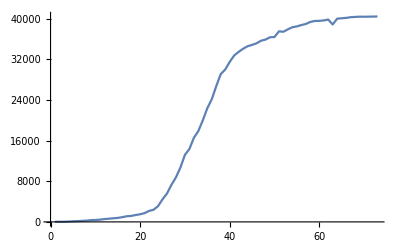

```mathematica
ListLinePlot@zikaTimeSeries[[All,2]]
```

#### Correct reporting errors in CDC data

Remove cases of non-continuity - eg if value at time t is less than at time t+2, but value at time t+1 does not fall between value at time t and at time t+2, replace value at time t+1 with the midpoint between t and t+2

```mathematica
For[i=1,i≤Length[zikaTimeSeries]-2,i++,
If[zikaTimeSeries[[i,2]]<=zikaTimeSeries[[i+2,2]]&&!(zikaTimeSeries[[i,2]]<=zikaTimeSeries[[i+1,2]]<=zikaTimeSeries[[i+2,2]]),
zikaTimeSeries[[i+1,2]]=(zikaTimeSeries[[i,2]]+zikaTimeSeries[[i+2,2]])/2,Continue[]]]
```

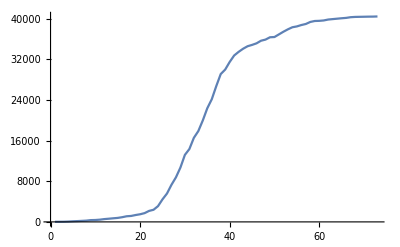

```mathematica
ListLinePlot@zikaTimeSeries[[All,2]]
```

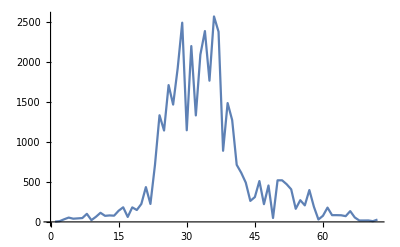

```mathematica
ListLinePlot@Differences@zikaTimeSeries[[All,2]]
```

#### Correct CDC epi curve to match CHKV attack rate

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Dropbox\Projects\Zika vaccine\Code\Fresh

Compute model-derived total population for Puerto Rico

```mathematica
prPop=First[pullAllPopulation[runCalibration["Puerto Rico",0.2,{βmf->0.1,MosqBirth->(365/7.8)*mosquitoPopulation["Puerto Rico"]}]]]
```

3.685×10^6

Compute the expansion factor

```mathematica
expansionFactor=(prPop*N@Mean@target)/Last[zikaTimeSeries[[All,2]]]
```

21.3987

Correct the Zika time series by the expansion factor

```mathematica
zikaTimeSeries=zikaTimeSeries[[All,2]]*expansionFactor;
```

#### Write corrected CDC epi curve

```mathematica
SetDirectory[NotebookDirectory[]];
Put[zikaTimeSeries,"zikaTimeSeries.dat"]
```

#### Read in corrected CDC epi curve

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
zikaTimeSeries=Get["zikaTimeSeries.dat"];
```

### Setup calibration functions

Compute the least-squares difference between the specified epi curve and Zika attack rate

```mathematica
Clear@findMinLSE
findMinLSE[solution_]:=
MinimalBy[
Table[{lag,
Sum[((entry-Mean[entry]).(entry-Mean[entry])),
{entry,Transpose[{solution,PadRight[Join[Table[0,{lag}],zikaTimeSeries],Length[solution],Last[zikaTimeSeries]]}]}]},
{lag,0,Length[solution]-Length[zikaTimeSeries]}],Last]
```

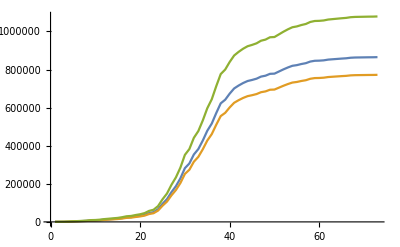

```mathematica
ListLinePlot[{zikaTimeSeries,zikaTimeSeries*(InverseCDF[target,0.025]/InverseCDF[target,0.5]),zikaTimeSeries*(InverseCDF[target,0.975]/InverseCDF[target,0.025])}]
```

Compute the solution, time series, lag, and sum-sqared-errors for a specified parameter set

```mathematica
Clear@computeParSet
computeParSet[betaHV_:0.1,parSet_:{}]:=
With[{solInf=pullAllInfections[runCalibration["Puerto Rico",betaHV,parSet]]},
With[{
lse=findMinLSE[solInf],
lowlse=Block[{zikaTimeSeries=zikaTimeSeries*(InverseCDF[target,0.025]/InverseCDF[target,0.5])},findMinLSE[solInf]],
highlse=Block[{zikaTimeSeries=zikaTimeSeries*(InverseCDF[target,0.975]/InverseCDF[target,0.5])},findMinLSE[solInf]]
},
Association[{
"parameters"->parSet,
"betaHV"->betaHV,
"timeSeries"->solInf,
"base"->Association[{
"lag"->lse[[1,1]],
"sse"->lse[[1,2]]}],
"lowCI"->Association[{
"lag"->lowlse[[1,1]],
"sse"->lowlse[[1,2]]}],
"highCI"->Association[{
"lag"->highlse[[1,1]],
"sse"->highlse[[1,2]]}]
}]
]
];
```

## Cluster run - calibrate transmission rate and amplitude / phase shift

### Overview

This section is designed to be run on the cluster.
It samples 3 parameters: 
1) The human-vector transmission rate betaHV
2) The seasonality amplitude
3) The seasonality phase

The range of parameters to be run is defined in the object parameterRange
This range is then divided into 100 subsets, such that the command line input (1-100) specifies which of the subsets to execute

Cluster results should be put into the subdirectory “Data/Calibration with seasonality”
The source code executed on the cluster is in the subdirectory “Data/Calibration with seasonality/src”

### Setup

#### First estimate target

Compute total population in PR at start of model

```mathematica
prPop=First@pullAllPopulation[runCalibration["Puerto Rico",0.1,{}]]
```

3.685×10^6

Record CHKV seroprevalence (Simmons et al EID)

```mathematica
prCHKV=0.235
```

0.235

Compute the outbreak size to target

```mathematica
targetOutbreakSize=prPop*prCHKV
```

865975.

As it doesn’t change, hard-code the outbreak size to avoid re-computing the population

```mathematica
targetOutbreakSize=865975.47
```

865975.

#### Define parameter ranges

Estimated range for betaHV

```mathematica
betaHVRange=Range[0.23,0.27,0.001];
```

```mathematica
Length@betaHVRange
```

41

Range for seasonality amplitude

```mathematica
amplRange=Range[0,19]/20;
```

Range for phase shift

```mathematica
phaseRange=Range[20]*Pi/10;
```

```mathematica
parameterRange=Flatten[
Table[{targetBeta->betaI,a->aI,b->bI},{betaI,betaHVRange},{aI,amplRange},{bI,phaseRange}],2];
```

```mathematica
Dimensions@parameterRange
```

{16400,3}

### Run calibration

#### Master loop

Initiate random seed based upon file tag

Loop over the assembly function 100x

```mathematica
Length[parameterRange]
```

16400

```mathematica
nRuns=(*Ceiling@*)Length[parameterRange]/100
```

164

```mathematica
clusterI=If[ClusterRun,ToExpression[$CommandLine[[2]]],1]
```

1

```mathematica
Print[AbsoluteTiming[
iterationResults=
Table[
(*computeParSet[parset]*)computeParSet[targetBeta/.parset,{MosqBirth->365/7.8*mosquitoPopulation["Puerto Rico"]*(1-(a/.parset)*Cos[t*2*Pi+(b/.parset)])}],
{parset,parameterRange[[
Floor[(clusterI-1)*nRuns+1];;
Floor[If[ClusterRun,Min[clusterI*nRuns,Length[parameterRange]],(clusterI-1)*nRuns+1]]]]}];
]
]
```

{13.0803,Null}

#### Output master loop results

Output the results in a single file

```mathematica
Put[iterationResults,"iterationResults"<>$CommandLine[[2]]<>".dat"];
```

```mathematica
Quit[]
```

## Evaluate cluster results

### Evaluate cluster results

#### Read in

```mathematica
SetDirectory[NotebookDirectory[]<>"/Data/Calibration with seasonality"]
```

D:\Dropbox\Projects\Zika vaccine\Code\Fresh\Data\Calibration with seasonality

```mathematica
Dynamic@i
```

```mathematica
results=Flatten[Table[If[FileExistsQ["iterationResults"<>ToString@i<>".dat"],Get["iterationResults"<>ToString@i<>".dat"],Nothing],{i,100}]];
```

```mathematica
Length@results
```

16400

```mathematica
sseRes=#["sse"]&/@results;
```

```mathematica
Min@sseRes
```

3.55722×10^10

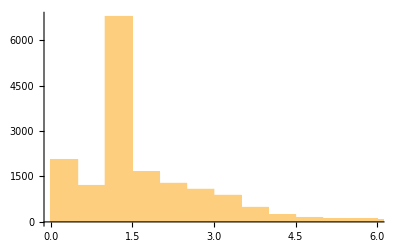

```mathematica
Histogram@sseRes
```

```mathematica
Min@sseRes
```

3.55722×10^10

#### Plot the best fit

```mathematica
Min@sseRes
```

3.55722×10^10

```mathematica
Position[results,Min@sseRes]
```

{{11922,Key[sse]},{11938,Key[sse]}}

```mathematica
minValue=Select[results,#["sse"]==Min@sseRes&][[1]];
```

```mathematica
minValue["betaHV"]
```

0.259

```mathematica
minValue["parameters"]
```

{MosqBirth→3.86369×10^8 (1-4/5 Cos[π/4+2 π t])}

```mathematica
Keys@minValue
```

{parameters,betaHV,timeSeries,lag,sse}

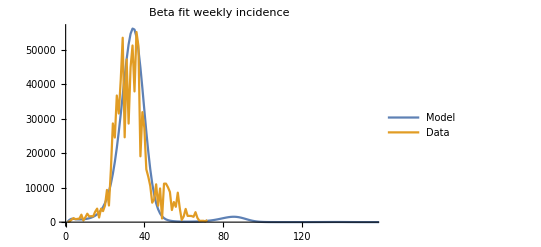

```mathematica
With[{res=minValue},
ListLinePlot[{Differences@res["timeSeries"],Join[Table[0,{res["lag"]}],Differences@zikaTimeSeries]},PlotLegends->{"Model","Data"},PlotRange->{{0,52*3},All},PlotLabel->"Beta fit weekly incidence",LabelStyle->Black]]
```

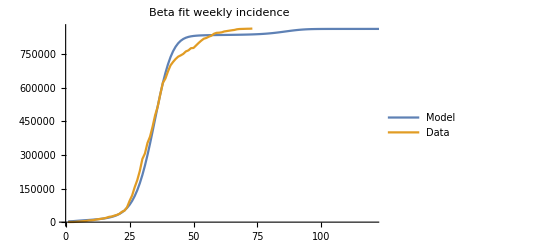

```mathematica
With[{res=minValue},
ListLinePlot[{res["timeSeries"],Join[Table[0,{res["lag"]}],zikaTimeSeries]},PlotLegends->{"Model","Data"},PlotRange->{{0,120},All},PlotLabel->"Beta fit weekly incidence",LabelStyle->Black]]
```

### Compute the parameters that best fit the 95% CI ranges of the PR data

```mathematica
findMinLSE[results[[1]]["timeSeries"]]
```

{{447,1.1387×10^13}}

```mathematica
Block[{zikaTimeSeries=zikaTimeSeries*(InverseCDF[target,0.025]/InverseCDF[target,0.5])},findMinLSE[results[[1]]["timeSeries"]]]
```

{{447,9.024×10^12}}

```mathematica
Block[{zikaTimeSeries=zikaTimeSeries*(InverseCDF[target,0.975]/InverseCDF[target,0.5])},findMinLSE[results[[1]]["timeSeries"]]]
```

{{447,1.4183×10^13}}

### Prepare plot for export

#### Read in dates

```mathematica
SetDirectory[NotebookDirectory[]<>"/InputData/PuertoRicoData"]
```

D:\Dropbox\Projects\Zika vaccine\Code\InputData\PuertoRicoData

Pull out all CSV files

```mathematica
csvfiles=Select[FileNames[],StringContainsQ[#,".csv"]&];
```

Pull out the date / week the file corresponds to

```mathematica
filedates=Sort[StringTake[#,{11,20}]&/@csvfiles];
```

#### Setup plot

Prepare the date strings

```mathematica
Clear@convertDate
convertDate[date_]:=DateString[date,{"MonthShort","-","DayShort","-","YearShort"}]
```

```mathematica
bestFitOffset=minValue["lag"];
bestFitTimeSeries=minValue["timeSeries"];
```

Additional weeks to be added at the end of the data series

```mathematica
addlWeeks=25;
```

```mathematica
fullDateSeries=convertDate/@
Join[Table[DatePlus[DateObject[filedates[[1]]],x],{x,-7*(bestFitOffset+1),-7,7}],DateObject/@filedates,Table[DatePlus[DateObject[filedates[[-1]]],x],{x,7,7*addlWeeks,7}]];
```

Display the plot

```mathematica
Length@fullDateSeries
```

99

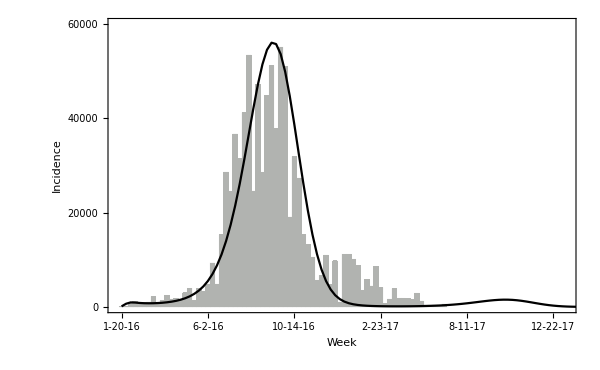

```mathematica
calibratedPlotIncidence=With[{
dataSeries=Join[Table[0,{bestFitOffset}],Differences@zikaTimeSeries],
modelSeries=Differences@bestFitTimeSeries},
Show[
BarChart[dataSeries,
ChartStyle->{ColorData["GrayTones"][0.75]},PlotRange->{{0,Length[fullDateSeries](*Length[dataSeries]+1+7*addlWeeks*)},All},Ticks->None,Axes->None],
ListLinePlot[modelSeries,PlotRange->All,
PlotStyle->Black,PlotRange->{{0,Length[fullDateSeries](*Length[dataSeries]+1+7*addlWeeks*)},All},Ticks->None],

PlotRange->{{0,Length[fullDateSeries](*Length[dataSeries]+1+7*addlWeeks*)},{0,60000}},

Frame->{True,True,False,False},FrameStyle->Black,FrameLabel->{"Week","Incidence"},
FrameTicks->{{{#,#,{0,0.01}}&/@Range[0,60000,20000],None},{{#,Rotate[fullDateSeries[[#]],Pi/4],{0,0.01}}&/@Range[1,Length@fullDateSeries,19],None}},

LabelStyle->Directive[Black,24],ImageSize->600
]
]
```

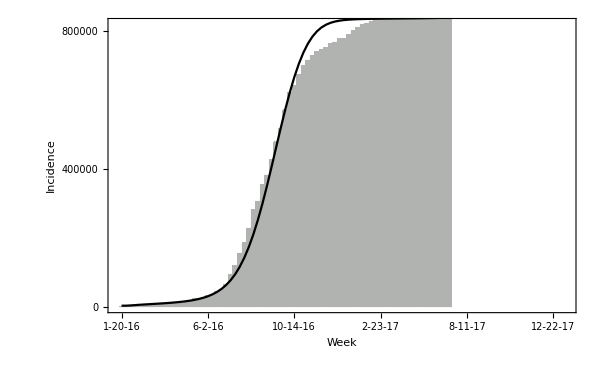

```mathematica
calibratedPlotCumulative=With[{
dataSeries=Join[Table[0,{bestFitOffset}],zikaTimeSeries],
modelSeries=bestFitTimeSeries},
Show[
BarChart[dataSeries,
ChartStyle->{ColorData["GrayTones"][0.75]},PlotRange->{{0,Length[fullDateSeries](*Length[dataSeries]+1+7*addlWeeks*)},All},Ticks->None,Axes->None],
ListLinePlot[modelSeries,PlotRange->All,
PlotStyle->Black,PlotRange->{{0,Length[fullDateSeries](*Length[dataSeries]+1+7*addlWeeks*)},All},Ticks->None],

PlotRange->{{0,Length[fullDateSeries](*Length[dataSeries]+1+7*addlWeeks*)},{0,820000}},

Frame->{True,True,False,False},FrameStyle->Black,FrameLabel->{"Week","Incidence"},
FrameTicks->{{{#,#,{0,0.01}}&/@Range[0,800000,400000],None},{{#,Rotate[fullDateSeries[[#]],Pi/4],{0,0.01}}&/@Range[1,Length@fullDateSeries,19],None}},

LabelStyle->Directive[Black,24],ImageSize->600
]
]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"/GeneratedResults/Validation"]
```

D:\Dropbox\Projects\Zika vaccine\Code\GeneratedResults\Validation

```mathematica
Export["validationFigureIncidence.jpg",calibratedPlotIncidence];
Export["validationFigureIncidence.tiff",calibratedPlotIncidence];

Export["validationFigureCumulative.jpg",calibratedPlotCumulative];
Export["validationFigureCumulative.tiff",calibratedPlotCumulative];
```